```mathematica
apple = FinancialData["NASDAQ:AAPL", "Close", {{2006, 1, 1}, {2015,1,1}}];
```

```mathematica
apple
```

{{{2006,1,3},9.98554},{{2006,1,4},10.0149},{{2006,1,5},9.93611},{{2006,1,6},10.1926},{{2006,1,9},10.1592},{{2006,1,10},10.8017},2253,{{2014,12,23},111.128},{{2014,12,24},110.605},{{2014,12,26},112.56},{{2014,12,29},112.481},{{2014,12,30},111.109},{{2014,12,31},108.995}}
 |  |  |  |

```mathematica
HurstR[data_] := Module[{zs},
zs = Accumulate[data - Mean[data]];
Max[zs] - Min[zs]
]
```

```mathematica
HurstS[data_] := StandardDeviation[data]
```

```mathematica
HurstRS[data_] := If[Abs[HurstS[data]] ≤ 10^-6, 1.0, HurstR[data] / HurstS[data]]
```

```mathematica
HurstExponent[data_] := Module[{n, chunkSize, tmp, helper, model, ndata}, 
n = 2^Round[Log[2, Length[data]]];
ndata = Drop[data,Length[data] - n];
helper = Function[{vs, size}, { Log[2.0, size], Log[2.0, Mean[Map[HurstRS, Partition[vs, size]]]]}];
chunkSize = NestWhileList[# / 2&, n, # >=4&];
tmp = Map[helper[ndata, #]&, chunkSize];
tmp = Take[tmp, Length[tmp] - 1];
model = LinearModelFit[tmp , x, x];
Print[tmp];
Print[model["BestFit"]];
Show[ListPlot[tmp], Plot[model["BestFit"], {x, 0, 20}]]
]
```

```mathematica
Length[apple]
```

2265

```mathematica
microsoft = FinancialData["NASDAQ:MSFT", "Close", {{2006, 1, 1}, {2015,1,1}}];
```

```mathematica
Length[microsoft]
```

2265

{{11.,5.79078},{10.,5.55893},{9.,4.79857},{8.,4.24113},{7.,3.73705},{6.,3.13955},{5.,2.61629},{4.,1.98696},{3.,1.30051},{2.,0.518301}}

-0.444184+0.586614 x

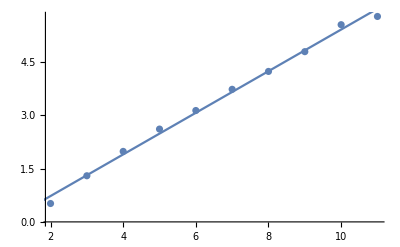

```mathematica
HurstExponent[Drop[Map[Last, apple], 1] - Take[Map[Last, apple], Length[apple] - 1]]
```

{{11.,5.621},{10.,5.18305},{9.,4.52926},{8.,3.99734},{7.,3.59088},{6.,3.002},{5.,2.46052},{4.,1.95925},{3.,1.29983},{2.,0.523331}}

-0.372571+0.552187 x

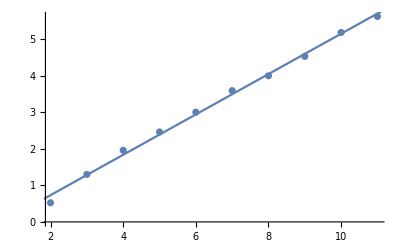

```mathematica
HurstExponent[Drop[Map[Last, microsoft], 1] - Take[Map[Last, microsoft], Length[microsoft] - 1]]
```

{{11.,8.08199},{10.,7.58497},{9.,6.83778},{8.,6.1246},{7.,5.48343},{6.,4.59325},{5.,3.60566},{4.,2.62058},{3.,1.57307},{2.,0.571179}}

-0.77652+0.843719 x

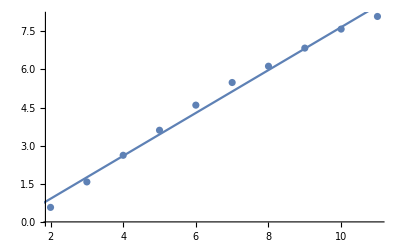

```mathematica
HurstExponent[Drop[Map[Last, microsoft], 30] - Take[Map[Last, microsoft], Length[microsoft] - 30]]
```

{{11.,5.621},{10.,5.18305},{9.,4.52926},{8.,3.99734},{7.,3.59088},{6.,3.002},{5.,2.46052},{4.,1.95925},{3.,1.29983},{2.,0.523331}}

-0.372571+0.552187 x

-Graphics-

{{11.,6.14936},{10.,5.70374},{9.,5.00481},{8.,4.46853},{7.,4.04572},{6.,3.43387},{5.,2.82048},{4.,2.25507},{3.,1.48583},{2.,0.584403}}

-0.301462+0.599483 x

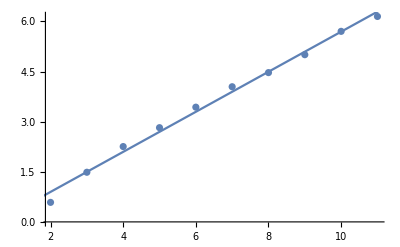

{{11.,6.46896},{10.,6.01801},{9.,5.28931},{8.,4.73487},{7.,4.31695},{6.,3.6633},{5.,3.02428},{4.,2.38114},{3.,1.57756},{2.,0.56662}}

-0.313766+0.633518 x

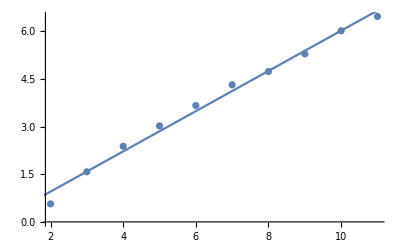

{{11.,6.66631},{10.,6.1983},{9.,5.48079},{8.,4.89806},{7.,4.48507},{6.,3.81821},{5.,3.14122},{4.,2.44957},{3.,1.60536},{2.,0.572573}}

-0.326454+0.655077 x

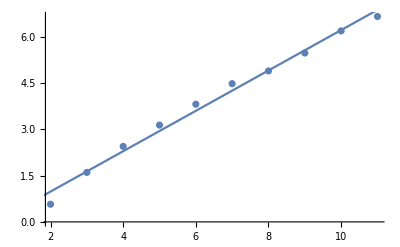

{{11.,6.83841},{10.,6.35272},{9.,5.64164},{8.,5.04092},{7.,4.62783},{6.,3.93924},{5.,3.23963},{4.,2.50902},{3.,1.60883},{2.,0.564658}}

-0.353237+0.675312 x

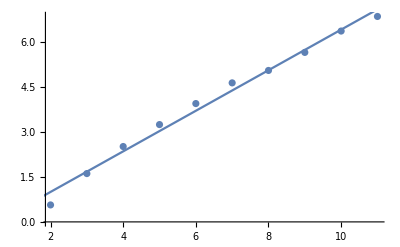

{{11.,6.98103},{10.,6.48388},{9.,5.78302},{8.,5.16074},{7.,4.75196},{6.,4.04464},{5.,3.32242},{4.,2.55794},{3.,1.58909},{2.,0.569718}}

-0.378798+0.692806 x

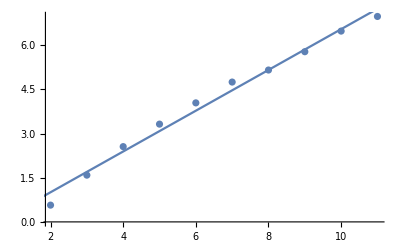

{{11.,7.09842},{10.,6.59659},{9.,5.89426},{8.,5.25847},{7.,4.84344},{6.,4.12444},{5.,3.37997},{4.,2.57828},{3.,1.5739},{2.,0.569779}}

-0.411468+0.708188 x

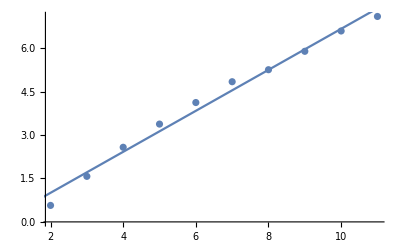

{{11.,7.2027},{10.,6.69941},{9.,6.00156},{8.,5.35289},{7.,4.9283},{6.,4.19367},{5.,3.4167},{4.,2.57428},{3.,1.55363},{2.,0.575433}}

-0.45163+0.723306 x

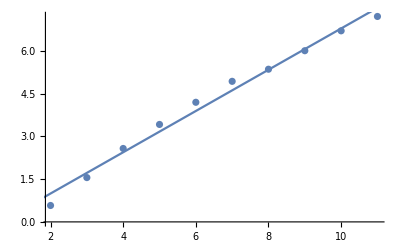

{{11.,7.30104},{10.,6.79611},{9.,6.0992},{8.,5.44515},{7.,5.00861},{6.,4.2547},{5.,3.46096},{4.,2.58641},{3.,1.53086},{2.,0.555993}}

-0.49556+0.738379 x

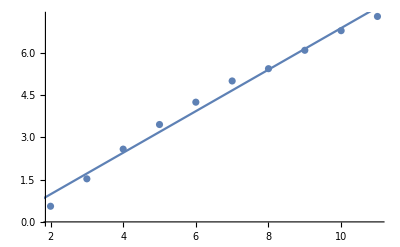

{{11.,7.38366},{10.,6.88567},{9.,6.18481},{8.,5.52748},{7.,5.07456},{6.,4.30605},{5.,3.48944},{4.,2.59353},{3.,1.54593},{2.,0.565783}}

-0.512532+0.748958 x

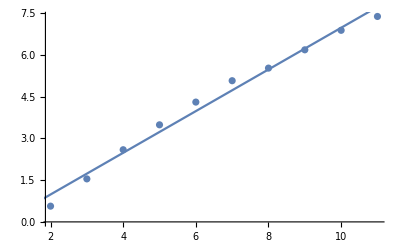

{{11.,7.4466},{10.,6.96219},{9.,6.25271},{8.,5.60542},{7.,5.12669},{6.,4.34732},{5.,3.50759},{4.,2.58351},{3.,1.54224},{2.,0.557888}}

-0.545087+0.759739 x

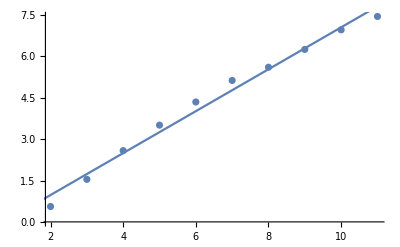

{{11.,7.5015},{10.,7.02168},{9.,6.31053},{8.,5.67333},{7.,5.16585},{6.,4.37535},{5.,3.51924},{4.,2.56246},{3.,1.55559},{2.,0.565599}}

-0.565263+0.76775 x

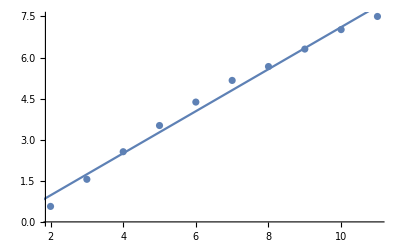

{{11.,7.54952},{10.,7.06938},{9.,6.35565},{8.,5.72641},{7.,5.19661},{6.,4.39211},{5.,3.52112},{4.,2.54697},{3.,1.56024},{2.,0.565547}}

-0.589479+0.775052 x

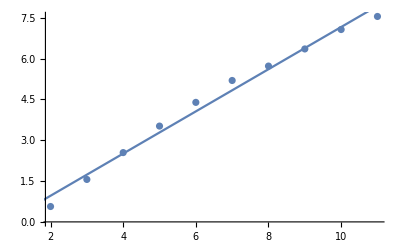

{{11.,7.59591},{10.,7.11712},{9.,6.40352},{8.,5.77647},{7.,5.23041},{6.,4.41475},{5.,3.539},{4.,2.54438},{3.,1.56675},{2.,0.570147}}

-0.602358+0.781262 x

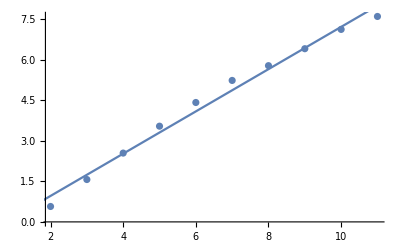

{{11.,7.6351},{10.,7.15818},{9.,6.446},{8.,5.82286},{7.,5.26003},{6.,4.4314},{5.,3.5479},{4.,2.55261},{3.,1.56048},{2.,0.561973}}

-0.622084+0.787652 x

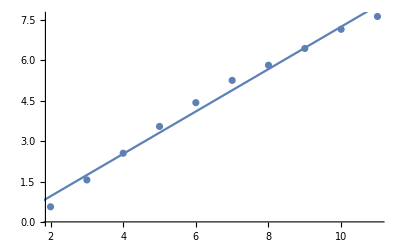

{{11.,7.67364},{10.,7.1966},{9.,6.48537},{8.,5.86126},{7.,5.28814},{6.,4.44711},{5.,3.55531},{4.,2.56837},{3.,1.55223},{2.,0.559284}}

-0.637293+0.793235 x

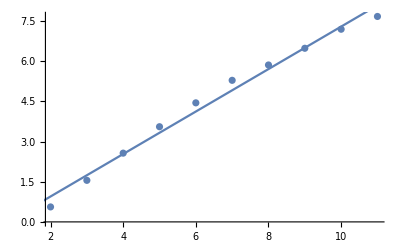

{{11.,7.71214},{10.,7.23697},{9.,6.52439},{8.,5.89536},{7.,5.31445},{6.,4.46533},{5.,3.55531},{4.,2.5731},{3.,1.54844},{2.,0.562225}}

-0.65314+0.798755 x

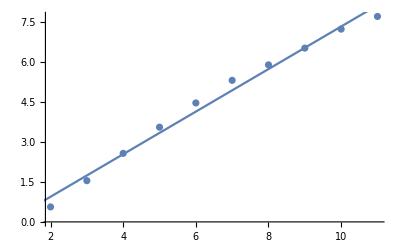

{{11.,7.74672},{10.,7.27074},{9.,6.55651},{8.,5.92088},{7.,5.33351},{6.,4.475},{5.,3.54385},{4.,2.57138},{3.,1.56161},{2.,0.552479}}

-0.671442+0.803802 x

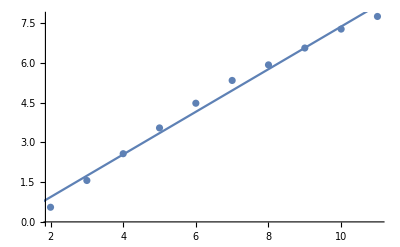

{{11.,7.78608},{10.,7.30931},{9.,6.59502},{8.,5.9494},{7.,5.35689},{6.,4.48575},{5.,3.55067},{4.,2.57335},{3.,1.56254},{2.,0.570553}}

-0.678941+0.808138 x

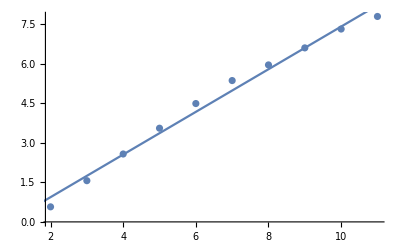

{{11.,7.81942},{10.,7.34562},{9.,6.6314},{8.,5.97439},{7.,5.37758},{6.,4.49645},{5.,3.55911},{4.,2.5765},{3.,1.56037},{2.,0.557443}}

-0.699044+0.813673 x

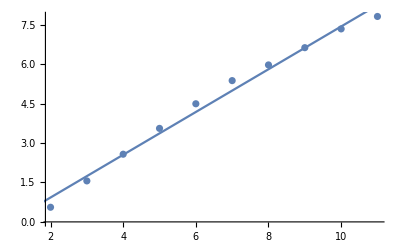

{{11.,7.8462},{10.,7.37815},{9.,6.66432},{8.,5.99578},{7.,5.3969},{6.,4.51513},{5.,3.57261},{4.,2.57449},{3.,1.54333},{2.,0.55618}}

-0.716015+0.818512 x

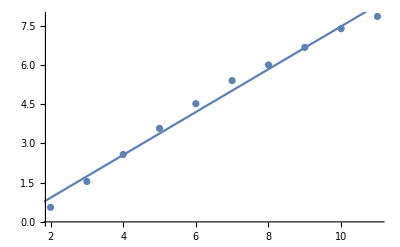

{{11.,7.87953},{10.,7.40732},{9.,6.69326},{8.,6.01891},{7.,5.41544},{6.,4.53659},{5.,3.57899},{4.,2.57092},{3.,1.53003},{2.,0.568782}}

-0.727673+0.822715 x

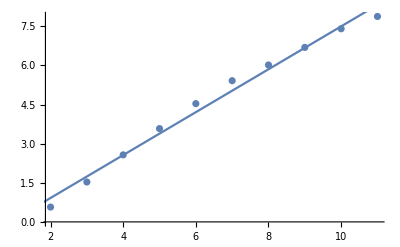

{{11.,7.90746},{10.,7.43305},{9.,6.72359},{8.,6.04241},{7.,5.43177},{6.,4.55098},{5.,3.59985},{4.,2.57147},{3.,1.55859},{2.,0.566879}}

-0.7251+0.825186 x

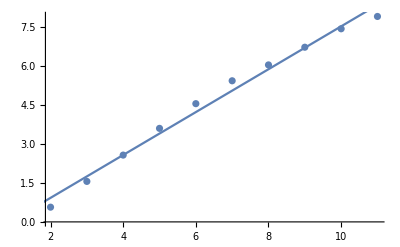

{{11.,7.93308},{10.,7.45637},{9.,6.74626},{8.,6.05825},{7.,5.44334},{6.,4.55418},{5.,3.60252},{4.,2.56369},{3.,1.52588},{2.,0.564042}}

-0.752364+0.830327 x

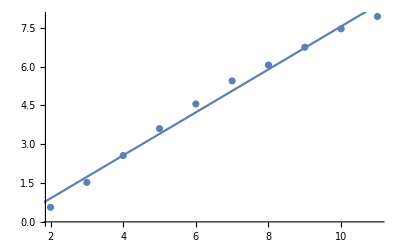

{{11.,7.95854},{10.,7.47915},{9.,6.76517},{8.,6.07094},{7.,5.45237},{6.,4.55149},{5.,3.59977},{4.,2.57321},{3.,1.54197},{2.,0.56073}}

-0.757975+0.832817 x

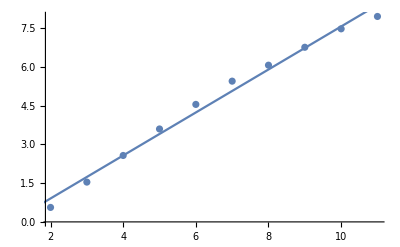

{{11.,7.983},{10.,7.50098},{9.,6.78379},{8.,6.08418},{7.,5.46125},{6.,4.55793},{5.,3.60123},{4.,2.57392},{3.,1.57676},{2.,0.564699}}

-0.753239+0.834156 x

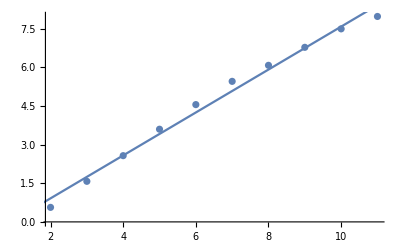

{{11.,8.00976},{10.,7.52156},{9.,6.80124},{8.,6.0956},{7.,5.468},{6.,4.56827},{5.,3.59794},{4.,2.57606},{3.,1.57926},{2.,0.572097}}

-0.759503+0.83669 x

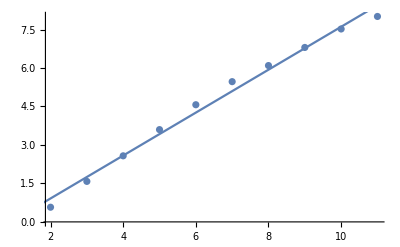

{{11.,8.03552},{10.,7.54405},{9.,6.81592},{8.,6.1038},{7.,5.47117},{6.,4.57868},{5.,3.59935},{4.,2.59537},{3.,1.57365},{2.,0.560981}}

-0.771057+0.839832 x

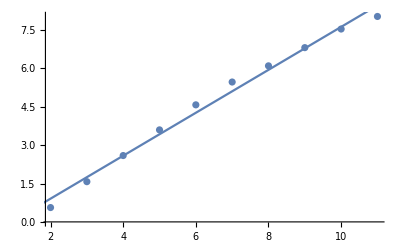

{{11.,8.0568},{10.,7.56426},{9.,6.82752},{8.,6.11526},{7.,5.47771},{6.,4.5887},{5.,3.6038},{4.,2.61966},{3.,1.57848},{2.,0.558225}}

-0.77082+0.841517 x

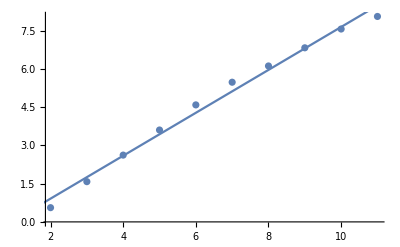

{{11.,8.08199},{10.,7.58497},{9.,6.83778},{8.,6.1246},{7.,5.48343},{6.,4.59325},{5.,3.60566},{4.,2.62058},{3.,1.57307},{2.,0.571179}}

-0.77652+0.843719 x

-Graphics-

```mathematica
For[i = 1, i ≤ 30, i++,
Print[HurstExponent[Drop[Map[Last, microsoft], i] - Take[Map[Last, microsoft], Length[microsoft] - i]]]]
```

```mathematica
china = Import["~/Downloads/000001.csv"]
```

{{ÈÕÆÚ,.b9ÉÆ±.b4úÂë,Ãû.b3Æ,ÊÕÅÌ.bcÛ},{2015-10-27,'000001,ÉÏÖ¤Ö¸Êý,3434.34},{2015-10-26,'000001,ÉÏÖ¤Ö¸Êý,3429.58},{2015-10-23,'000001,ÉÏÖ¤Ö¸Êý,3412.43},{2015-10-22,'000001,ÉÏÖ¤Ö¸Êý,3368.74},{2015-10-21,'000001,ÉÏÖ¤Ö¸Êý,3320.68},6067,{1990-12-26,'000001,ÉÏÖ¤Ö¸Êý,125.27},{1990-12-25,'000001,ÉÏÖ¤Ö¸Êý,120.25},{1990-12-24,'000001,ÉÏÖ¤Ö¸Êý,114.55},{1990-12-21,'000001,ÉÏÖ¤Ö¸Êý,109.13},{1990-12-20,'000001,ÉÏÖ¤Ö¸Êý,104.39},{1990-12-19,'000001,ÉÏÖ¤Ö¸Êý,99.98}}
 |  |  |  |

```mathematica
chinaPrice = Reverse[Map[Last, china⟦2;;⟧]];
```

```mathematica
Length[chinaPrice]
```

6078

```mathematica
chinaPrice = Drop[chinaPrice, 6078 - 2236];
```

```mathematica
Length[chinaPrice]
```

2236

{{11.,6.14705},{10.,5.86503},{9.,4.95113},{8.,4.38157},{7.,3.74455},{6.,3.1564},{5.,2.48693},{4.,1.94527},{3.,1.28448},{2.,0.520815}}

-0.648698+0.630311 x

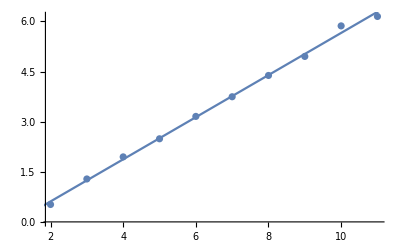

```mathematica
HurstExponent[Drop[chinaPrice, 1] - Take[chinaPrice, Length[chinaPrice] - 1]]
```

{{11.,6.14705},{10.,5.86503},{9.,4.95113},{8.,4.38157},{7.,3.74455},{6.,3.1564},{5.,2.48693},{4.,1.94527},{3.,1.28448},{2.,0.520815}}

-0.648698+0.630311 x

-Graphics-

{{11.,6.60064},{10.,6.3086},{9.,5.40556},{8.,4.83189},{7.,4.19295},{6.,3.5769},{5.,2.86285},{4.,2.27532},{3.,1.50101},{2.,0.589642}}

-0.515901+0.666221 x

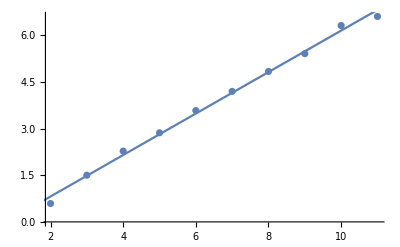

{{11.,6.90887},{10.,6.61884},{9.,5.71046},{8.,5.11222},{7.,4.46166},{6.,3.81251},{5.,3.08604},{4.,2.44109},{3.,1.59333},{2.,0.567667}}

-0.511798+0.698933 x

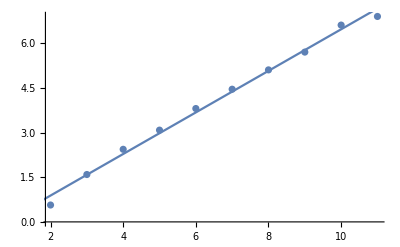

{{11.,7.09164},{10.,6.81307},{9.,5.89998},{8.,5.28716},{7.,4.62146},{6.,3.97177},{5.,3.22823},{4.,2.5323},{3.,1.62087},{2.,0.564169}}

-0.515263+0.719743 x

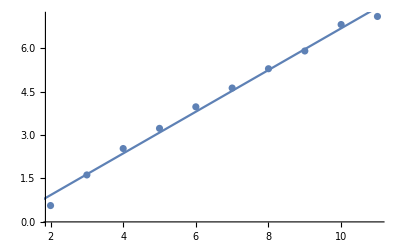

{{11.,7.21338},{10.,6.93939},{9.,6.02937},{8.,5.41607},{7.,4.73063},{6.,4.08551},{5.,3.32083},{4.,2.58047},{3.,1.62363},{2.,0.571822}}

-0.521849+0.734301 x

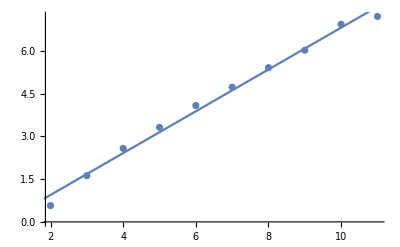

{{11.,7.31358},{10.,7.03847},{9.,6.13535},{8.,5.5207},{7.,4.82019},{6.,4.16264},{5.,3.38853},{4.,2.61092},{3.,1.60111},{2.,0.562133}}

-0.549815+0.748489 x

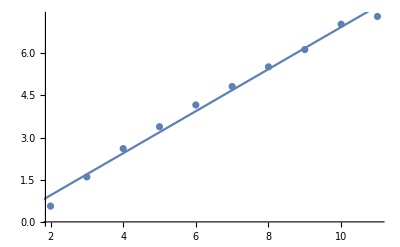

{{11.,7.4152},{10.,7.14073},{9.,6.24338},{8.,5.61763},{7.,4.90198},{6.,4.23933},{5.,3.44099},{4.,2.64342},{3.,1.60291},{2.,0.572274}}

-0.563866+0.760869 x

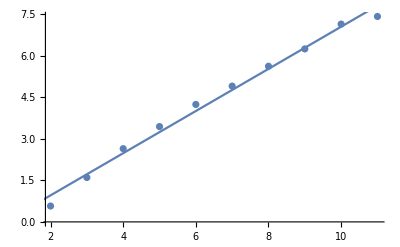

{{11.,7.49832},{10.,7.22214},{9.,6.32798},{8.,5.69253},{7.,4.96541},{6.,4.30606},{5.,3.47541},{4.,2.65113},{3.,1.60561},{2.,0.554834}}

-0.592864+0.772739 x

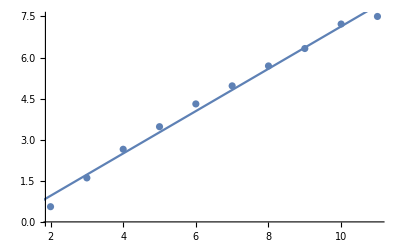

{{11.,7.56695},{10.,7.28851},{9.,6.39982},{8.,5.76044},{7.,5.02712},{6.,4.36386},{5.,3.50431},{4.,2.65218},{3.,1.61156},{2.,0.557753}}

-0.608224+0.781765 x

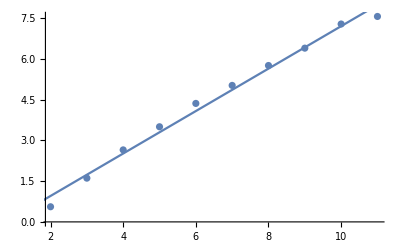

{{11.,7.63651},{10.,7.35583},{9.,6.47017},{8.,5.82256},{7.,5.08217},{6.,4.41231},{5.,3.53866},{4.,2.64213},{3.,1.59591},{2.,0.566661}}

-0.632949+0.791575 x

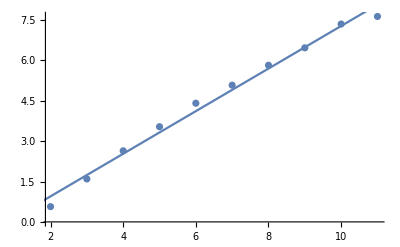

{{11.,7.69955},{10.,7.41921},{9.,6.53242},{8.,5.87814},{7.,5.12716},{6.,4.45165},{5.,3.5724},{4.,2.62747},{3.,1.58552},{2.,0.561758}}

-0.662094+0.801173 x

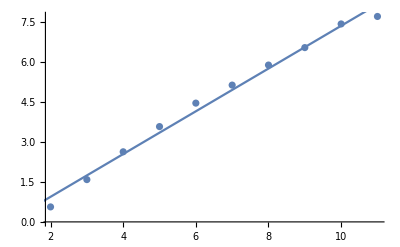

{{11.,7.75227},{10.,7.47489},{9.,6.58443},{8.,5.92328},{7.,5.16434},{6.,4.48601},{5.,3.59502},{4.,2.59745},{3.,1.5769},{2.,0.569179}}

-0.687961+0.809283 x

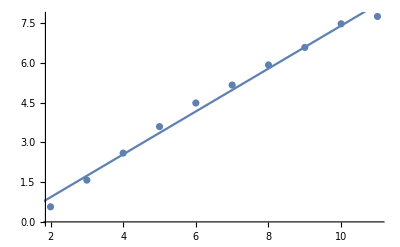

{{11.,7.7959},{10.,7.52012},{9.,6.62835},{8.,5.96416},{7.,5.19851},{6.,4.51633},{5.,3.62205},{4.,2.59275},{3.,1.58063},{2.,0.567032}}

-0.700796+0.815289 x

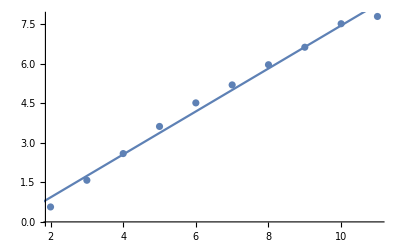

{{11.,7.83298},{10.,7.55939},{9.,6.6682},{8.,5.99797},{7.,5.22652},{6.,4.54259},{5.,3.63286},{4.,2.58328},{3.,1.56222},{2.,0.558034}}

-0.727722+0.822173 x

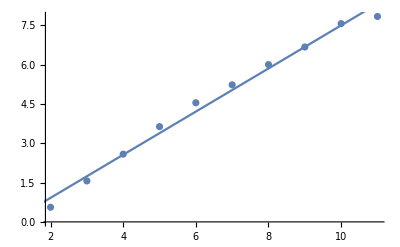

{{11.,7.87677},{10.,7.60103},{9.,6.70918},{8.,6.03281},{7.,5.24786},{6.,4.56623},{5.,3.63951},{4.,2.57876},{3.,1.57235},{2.,0.563117}}

-0.739978+0.827498 x

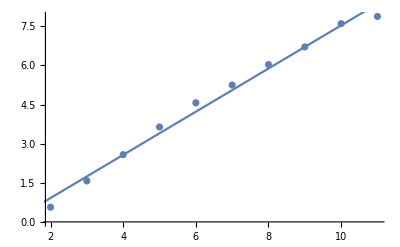

{{11.,7.91287},{10.,7.6389},{9.,6.74423},{8.,6.0637},{7.,5.26434},{6.,4.58612},{5.,3.64333},{4.,2.57681},{3.,1.59024},{2.,0.558251}}

-0.751248+0.832173 x

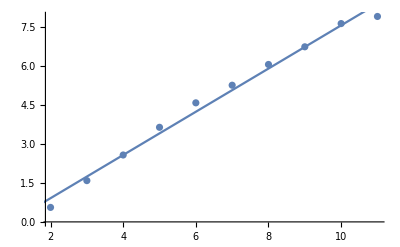

{{11.,7.94226},{10.,7.67197},{9.,6.7751},{8.,6.09072},{7.,5.28097},{6.,4.6003},{5.,3.63618},{4.,2.56734},{3.,1.59746},{2.,0.567136}}

-0.762665+0.836247 x

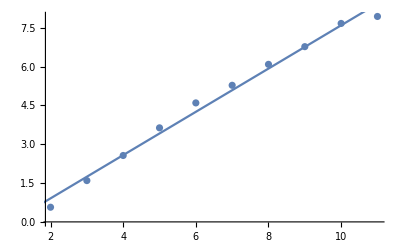

{{11.,7.97107},{10.,7.70265},{9.,6.80559},{8.,6.11909},{7.,5.30032},{6.,4.61141},{5.,3.62948},{4.,2.58289},{3.,1.59521},{2.,0.562694}}

-0.775849+0.840598 x

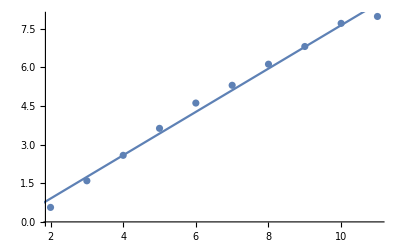

{{11.,7.9973},{10.,7.73109},{9.,6.83137},{8.,6.1474},{7.,5.31849},{6.,4.6163},{5.,3.63018},{4.,2.59424},{3.,1.58737},{2.,0.565426}}

-0.786936+0.844439 x

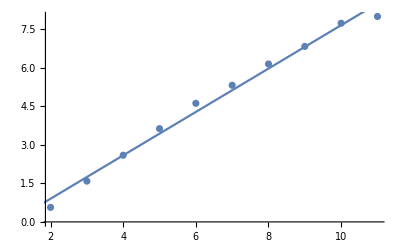

{{11.,8.02628},{10.,7.76052},{9.,6.85693},{8.,6.17603},{7.,5.33395},{6.,4.62519},{5.,3.63248},{4.,2.59575},{3.,1.5848},{2.,0.573372}}

-0.796709+0.84819 x

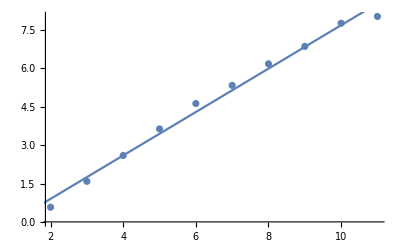

{{11.,8.05317},{10.,7.78531},{9.,6.87902},{8.,6.20039},{7.,5.34882},{6.,4.63044},{5.,3.64392},{4.,2.59081},{3.,1.57624},{2.,0.566839}}

-0.814023+0.852541 x

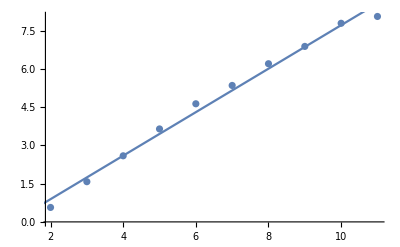

{{11.,8.07453},{10.,7.80545},{9.,6.89915},{8.,6.22269},{7.,5.36186},{6.,4.62768},{5.,3.64411},{4.,2.58638},{3.,1.57891},{2.,0.569366}}

-0.824072+0.855551 x

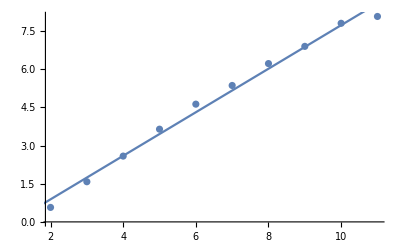

{{11.,8.09581},{10.,7.82782},{9.,6.92158},{8.,6.24508},{7.,5.3714},{6.,4.62492},{5.,3.65194},{4.,2.5935},{3.,1.58675},{2.,0.568677}}

-0.829355+0.85817 x

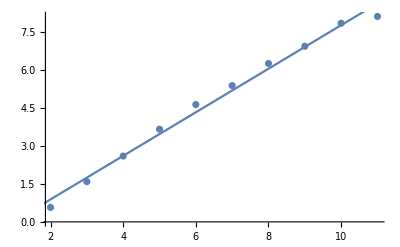

{{11.,8.11872},{10.,7.85049},{9.,6.94219},{8.,6.26606},{7.,5.38342},{6.,4.62787},{5.,3.65677},{4.,2.59694},{3.,1.59082},{2.,0.562274}}

-0.839713+0.861426 x

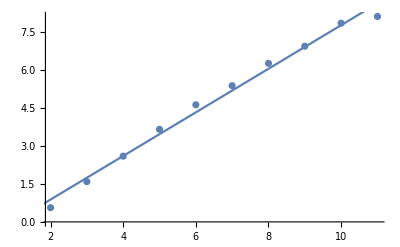

{{11.,8.13708},{10.,7.86999},{9.,6.96045},{8.,6.28738},{7.,5.39704},{6.,4.63214},{5.,3.66656},{4.,2.59341},{3.,1.59118},{2.,0.568948}}

-0.844297+0.863802 x

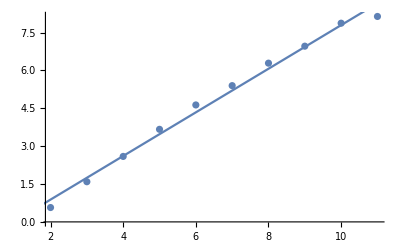

{{11.,8.15453},{10.,7.88719},{9.,6.97783},{8.,6.30695},{7.,5.40941},{6.,4.63673},{5.,3.66089},{4.,2.58124},{3.,1.57583},{2.,0.567963}}

-0.863483+0.867591 x

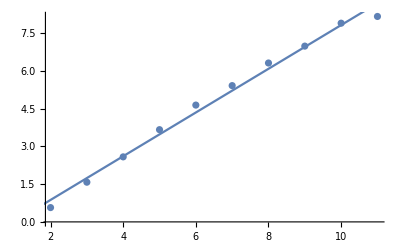

{{11.,8.17428},{10.,7.90566},{9.,6.99506},{8.,6.32462},{7.,5.41931},{6.,4.63766},{5.,3.66212},{4.,2.59603},{3.,1.56817},{2.,0.566174}}

-0.87205+0.870301 x

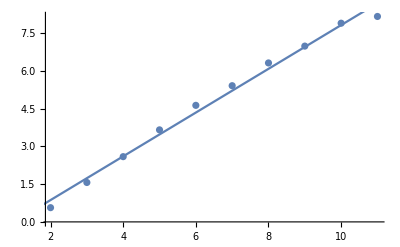

{{11.,8.19467},{10.,7.92378},{9.,7.01126},{8.,6.34155},{7.,5.42824},{6.,4.63275},{5.,3.66363},{4.,2.58717},{3.,1.56611},{2.,0.562426}}

-0.887228+0.873598 x

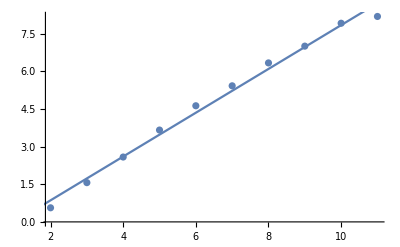

{{11.,8.2122},{10.,7.93928},{9.,7.02552},{8.,6.35512},{7.,5.4361},{6.,4.6276},{5.,3.65243},{4.,2.58432},{3.,1.55853},{2.,0.568472}}

-0.899673+0.876251 x

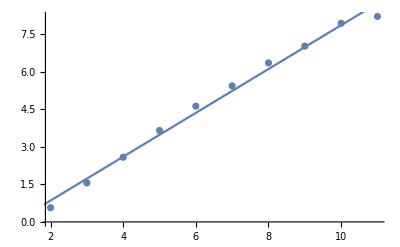

{{11.,8.22933},{10.,7.95433},{9.,7.0392},{8.,6.36825},{7.,5.44195},{6.,4.62925},{5.,3.64734},{4.,2.59491},{3.,1.57554},{2.,0.561727}}

-0.902301+0.877921 x

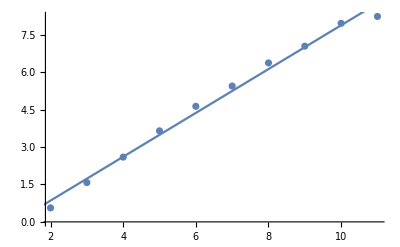

```mathematica
For[i = 1, i ≤ 30, i++,
Print[HurstExponent[Drop[chinaPrice, i] - Take[chinaPrice, Length[chinaPrice] - i]]]]
```

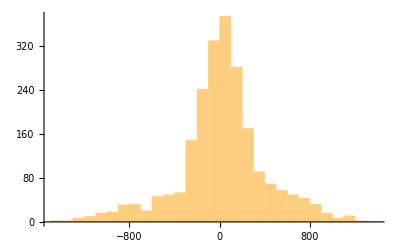

```mathematica
Histogram[Drop[chinaPrice, 30] - Take[chinaPrice , Length[chinaPrice] - 30]]
```

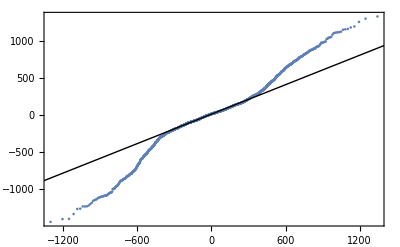

```mathematica
QuantilePlot[Drop[chinaPrice, 30] - Take[chinaPrice , Length[chinaPrice] - 30]]
```

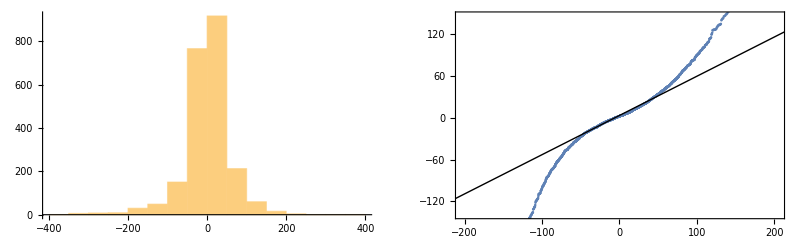

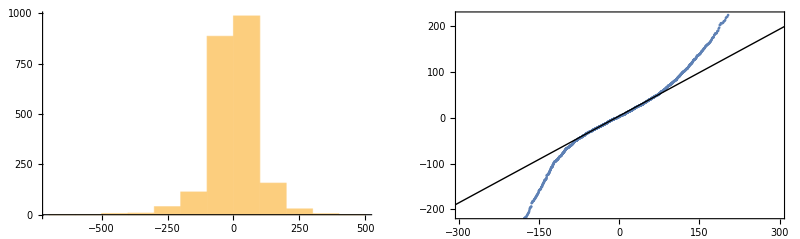

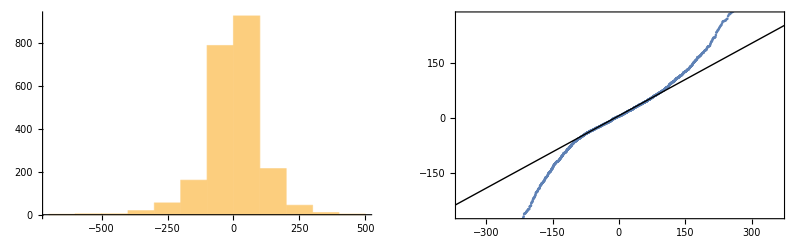

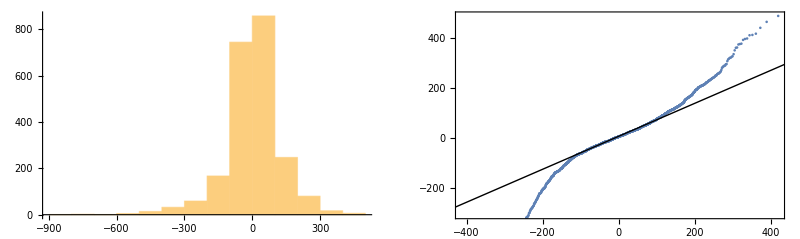

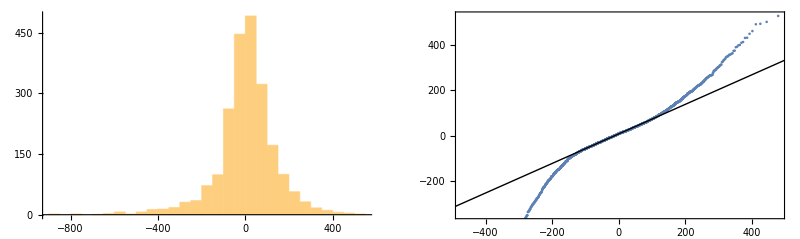

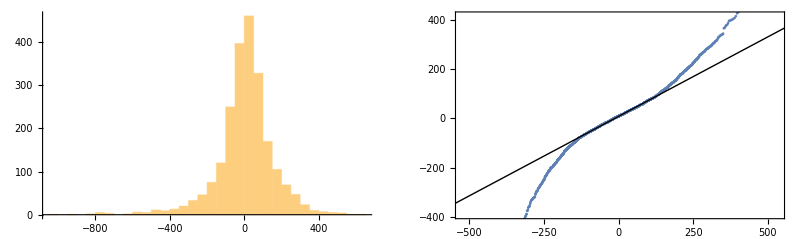

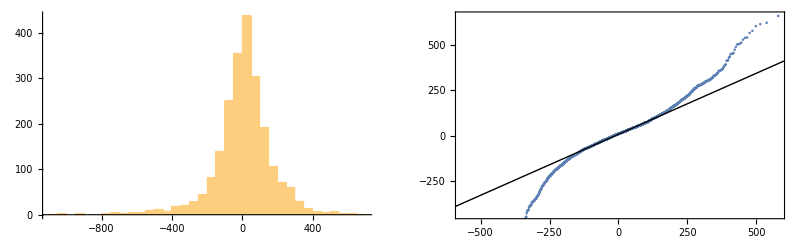

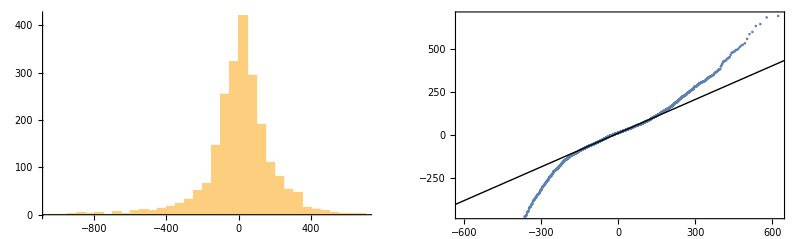

```mathematica
For[i = 1, i ≤ 60, i++,
Print[GraphicsRow[{Histogram[Drop[chinaPrice, i] - Take[chinaPrice , Length[chinaPrice] - i]], QuantilePlot[Drop[chinaPrice, i] - Take[chinaPrice , Length[chinaPrice] - i]]}]]]
```

```mathematica
Manipulate[
HurstR[data_] := Module[{zs},
zs = Accumulate[data - Mean[data]];
Max[zs] - Min[zs]
];
HurstS[data_] := StandardDeviation[data];
HurstRS[data_] := If[Abs[HurstS[data]] ≤ 10^-6, 1.0, HurstR[data] / HurstS[data]];
HurstExponent[data_] := Module[{n, chunkSize, tmp, helper, model, ndata}, 
n = 2^Round[Log[2, Length[data]]];
ndata = Drop[data,Length[data] - n];
helper = Function[{vs, size}, { Log[2.0, size], Log[2.0, Mean[Map[HurstRS, Partition[vs, size]]]]}];
chunkSize = NestWhileList[# / 2&, n, # >=4&];
tmp = Map[helper[ndata, #]&, chunkSize];
tmp = Take[tmp, Length[tmp] - 1];
model = LinearModelFit[tmp , x, x];
Show[ListPlot[tmp], Plot[model["BestFit"], {x, 0, 20}, PlotLegends-> {model["BestFit"]}]]
];
companyMap = <| "Apple" -> "NASDAQ:AAPL", "Google" -> "NASDAQ:GOOG", "Microsoft" -> "NASDAQ:MSFT", "Baidu" -> "NASDAQ:BIDU", "IBM" -> "NYSE:IBM", "HP"-> "NYSE:HP"|>;
prices =Map[Last, FinancialData[Lookup[companyMap, company], "Close", {{2006, 1, 1}, {2015,1,1}}]];
Column[{QuantilePlot[Drop[prices, n] - Take[prices, Length[prices] - n]],Histogram[Drop[prices, n] - Take[prices, Length[prices] - n]],HurstExponent[Drop[prices, n] - Take[prices, Length[prices] - n]]}],
{company, {"Apple", "Microsoft", "Google", "Baidu", "IBM", "HP"}},
{n, 1, 30, 1}]
```

Last::normal: Nonatomic expression expected at position 1 in Last["NotAvailable"].

QuantilePlot::ldata: 0 is not a valid dataset, distribution, or a valid list of datasets and distributions.

Histogram::ldata: 0 is not a valid dataset or list of datasets.

Drop::normal: Nonatomic expression expected at position 1 in Drop[0, 0].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Drop[0, 0], 0].

StandardDeviation::rectt: Rectangular array expected at position 1 in StandardDeviation[0].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[If[Abs[StandardDeviation[Drop[0, 0]]] ≤ 1/1000000, 1., HurstR[Drop[0, 0]]/HurstS[Drop[0, 0]]], If[Abs[StandardDeviation[0]] ≤ 1/1000000, 1., HurstR[0]/HurstS[0]]].

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit :: notdata will be suppressed during this calculation.

```mathematica
CloudDeploy[Manipulate[
HurstR[data_] := Module[{zs},
zs = Accumulate[data - Mean[data]];
Max[zs] - Min[zs]
];
HurstS[data_] := StandardDeviation[data];
HurstRS[data_] := If[Abs[HurstS[data]] ≤ 10^-6, 1.0, HurstR[data] / HurstS[data]];
HurstExponent[data_] := Module[{n, chunkSize, tmp, helper, model, ndata}, 
n = 2^Round[Log[2, Length[data]]];
ndata = Drop[data,Length[data] - n];
helper = Function[{vs, size}, { Log[2.0, size], Log[2.0, Mean[Map[HurstRS, Partition[vs, size]]]]}];
chunkSize = NestWhileList[# / 2&, n, # >=4&];
tmp = Map[helper[ndata, #]&, chunkSize];
tmp = Take[tmp, Length[tmp] - 1];
model = LinearModelFit[tmp , x, x];
Show[ListPlot[tmp], Plot[model["BestFit"], {x, 0, 20}, PlotLegends-> {model["BestFit"]}]]
];
companyMap = <| "Apple" -> "NASDAQ:AAPL", "Google" -> "NASDAQ:GOOG", "Microsoft" -> "NASDAQ:MSFT", "Baidu" -> "NASDAQ:BIDU", "IBM" -> "NYSE:IBM", "HP"-> "NYSE:HP"|>;
prices =Map[Last, FinancialData[Lookup[companyMap, company], "Close", {{2006, 1, 1}, {2015,1,1}}]];
Column[{QuantilePlot[Drop[prices, n] - Take[prices, Length[prices] - n]],Histogram[Drop[prices, n] - Take[prices, Length[prices] - n]],HurstExponent[Drop[prices, n] - Take[prices, Length[prices] - n]]}],
{company, {"Apple", "Microsoft", "Google", "Baidu", "IBM", "HP"}},
{n, 1, 30, 1}], Permissions -> "Public"
]
```

CloudObject[]

```mathematica
?Map
```

Map[f,expr] or f/@expr applies f to each element on the first level in expr. 
Map[f,expr,levelspec] applies f to parts of expr specified by levelspec. 
Map[f] represents an operator form of Map that can be applied to an expression.